```mathematica
U=UniformDistribution[];
```

```mathematica
pl1=Plot3D[CDF[CopulaDistribution["Minimal",{U,U}],{u,v}],{u,0,1},{v,0,1},BaseStyle->{FontSize->14},AxesLabel->{u,v}(*,PlotLabel->"Lower bound copula"*)]
```

-Graphics3D-

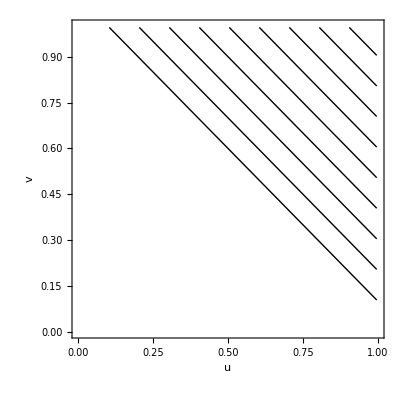

```mathematica
pl1b=ContourPlot[CDF[CopulaDistribution["Minimal",{U,U}],{u,v}],{u,0,1},{v,0,1},BaseStyle->{FontSize->14},ContourShading->None,ContourStyle->Thick,FrameLabel->{u,v}(*,PlotLabel->"Lower bound copula"*)]
```

```mathematica
Simplify[CDF[CopulaDistribution["Minimal",{U,U}],{u,v}],0≤u≤1&&0≤v≤1]
```

max(0,u+v-1)

```mathematica
Simplify[PDF[CopulaDistribution["Minimal",{U,U}],{u,v}],0≤u≤1&&0≤v≤1]
```

PDF[CopulaDistribution[Minimal,{UniformDistribution[{0,1}],UniformDistribution[{0,1}]}],{u,v}]

```mathematica
PDF[CopulaDistribution["Minimal",{U,U}],{u,v}]
```

PDF[CopulaDistribution[Minimal,{UniformDistribution[{0,1}],UniformDistribution[{0,1}]}],{u,v}]

```mathematica
pl2=Plot3D[CDF[CopulaDistribution["Maximal",{U,U}],{u,v}],{u,0,1},{v,0,1},BaseStyle->{FontSize->14},AxesLabel->{u,v}(*,PlotLabel->"Upper bound copulas"*)]
```

-Graphics3D-

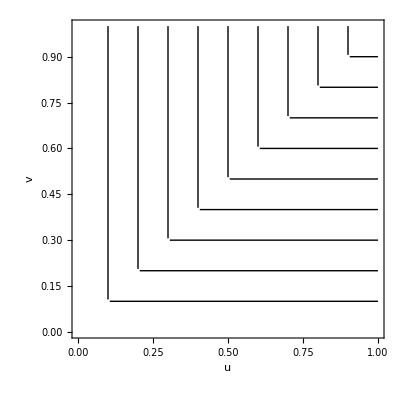

```mathematica
pl2b=ContourPlot[CDF[CopulaDistribution["Maximal",{U,U}],{u,v}],{u,0,1},{v,0,1},BaseStyle->{FontSize->14},ContourStyle->Thick,FrameLabel->{u,v},(*PlotLabel->"Upper bound copulas",*)ContourShading->None]
```

```mathematica
Simplify[CDF[CopulaDistribution["Maximal",{U,U}],{u,v}],0≤u≤1&&0≤v≤1]
```

min(u,v)

```mathematica
pl3=Plot3D[CDF[CopulaDistribution["Product",{U,U}],{u,v}],{u,0,1},{v,0,1},BaseStyle->{FontSize->14},AxesLabel->{u,v}(*, PlotLabel->"Product (Independence) copula"*)]
```

-Graphics3D-

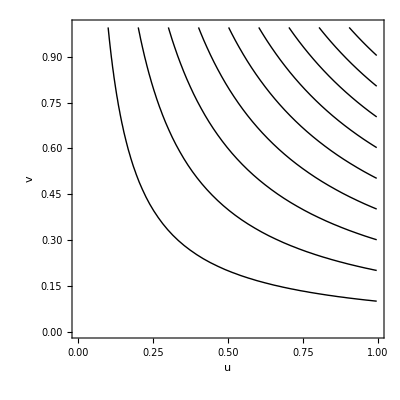

```mathematica
pl3b=ContourPlot[CDF[CopulaDistribution["Product",{U,U}],{u,v}],{u,0,1},{v,0,1},BaseStyle->{FontSize->14},ContourStyle->Thick,FrameLabel->{u,v}, (*PlotLabel->"Product (Independence) copula",*)ContourShading->None]
```

```mathematica
Simplify[CDF[CopulaDistribution["Product",{U,U}],{u,v}],0≤u≤1&&0≤v≤1]
```

u v

Probability density function:

```mathematica
pl4=Plot3D[PDF[CopulaDistribution[{"Binormal",.5},{U,U}], {x,y}],{x,0,1},{y,0,1},BaseStyle->{FontSize->14},AxesLabel->{u,v}(*,PlotLabel->"Gaussian (Normal) copula"*)]
```

-Graphics3D-

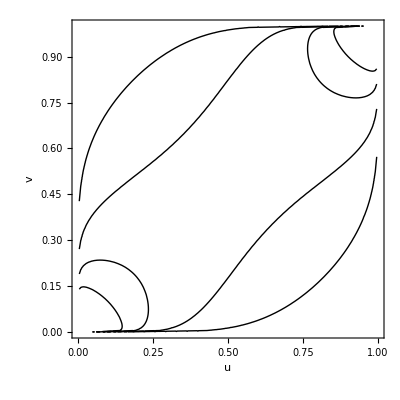

```mathematica
pl4b=ContourPlot[PDF[CopulaDistribution[{"Binormal",.5},{U,U}], {x,y}],{x,0,1},{y,0,1},BaseStyle->{FontSize->14},ContourStyle->Thick,AxesLabel->{u,v},(*PlotLabel->"Gaussian (Normal) copula",*)ContourShading->None]
```

```mathematica
Ndist=NormalDistribution[];pl5=Plot3D[PDF[CopulaDistribution[{"Binormal",.5},{Ndist,Ndist}], {x,y}],{x,-4,4},{y,-4,4},BaseStyle->{FontSize->14},PlotRange->All,AxesLabel->{x,y}(*, PlotLabel->"Bivariate Normal density"*)]
```

-Graphics3D-

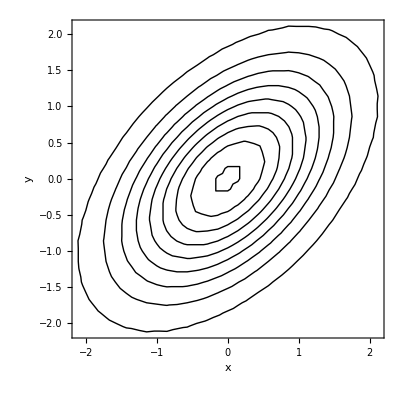

```mathematica
pl5b=ContourPlot[PDF[CopulaDistribution[{"Binormal",.5},{Ndist,Ndist}], {x,y}],{x,-4,4},{y,-4,4},BaseStyle->{FontSize->14},ContourStyle->Thick,PlotRange->All,AxesLabel->{x,y}, (*PlotLabel->"Bivariate Normal density",*)ContourShading->None]
```

```mathematica
Export["~/Documents/tex/scripts/riskmodelling/pics/copulas/minimal.eps", pl1,ImageResolution->300]
Export["~/Documents/tex/scripts/riskmodelling/pics/copulas/minimalb.eps", pl1b,ImageResolution->300]
Export["~/Documents/tex/scripts/riskmodelling/pics/copulas/maximal.eps", pl2,ImageResolution->300]
Export["~/Documents/tex/scripts/riskmodelling/pics/copulas/maximalb.eps", pl2b,ImageResolution->300]
Export["~/Documents/tex/scripts/riskmodelling/pics/copulas/product.eps", pl3,ImageResolution->300]
Export["~/Documents/tex/scripts/riskmodelling/pics/copulas/productb.eps", pl3b,ImageResolution->300]
Export["~/Documents/tex/scripts/riskmodelling/pics/copulas/normal1.eps", pl4,ImageResolution->300]Export["~/Documents/tex/scripts/riskmodelling/pics/copulas/normal2.eps", pl5,ImageResolution->300]
```

~/Documents/tex/scripts/riskmodelling/pics/copulas/minimal.eps

~/Documents/tex/scripts/riskmodelling/pics/copulas/minimalb.eps

~/Documents/tex/scripts/riskmodelling/pics/copulas/maximal.eps

~/Documents/tex/scripts/riskmodelling/pics/copulas/maximalb.eps

~/Documents/tex/scripts/riskmodelling/pics/copulas/product.eps

~/Documents/tex/scripts/riskmodelling/pics/copulas/productb.eps

~/Documents/tex/scripts/riskmodelling/pics/copulas/normal1.eps ~/Documents/tex/scripts/riskmodelling/pics/copulas/normal2.eps

```mathematica
Σ={{1,ρ},{ρ,1}};
Simplify[PDF[MultivariateTDistribution[Σ,ν],{x,y}]]
```

(√(1-ρ^2) (ν+2)/2 ((-ν ρ^2+ν+x^2-2 ρ x y+y^2)/(ν-ν ρ^2))^(-ν/2-1))/(π (ν-ν ρ^2) ν/2)

```mathematica
Simplify[{{s,t}}. Inverse[Σ]. {{s},{t}}]
```

(1.8809 | (maturity n | 1 | 2 | 3
interest rate (in %) r_n | 4% | 5% | 6%)).(1/(1-ρ^2) | ρ/(ρ^2-1)
ρ/(ρ^2-1) | 1/(1-ρ^2)).(1.8809
(maturity n | 1 | 2 | 3
interest rate (in %) r_n | 4% | 5% | 6%))

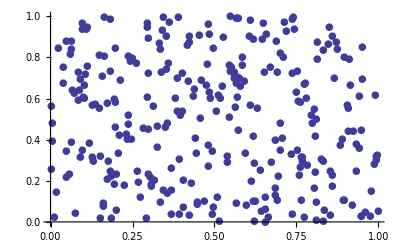

```mathematica
U=RandomVariate[UniformDistribution[],500];
V=RandomVariate[UniformDistribution[],500];
pl1=ListPlot[{U,V}ᵀ,BaseStyle->{FontSize->14},PlotLabel->"Independent U(0,1)-random numbers",PlotMarkers->{Automatic,10}]
```

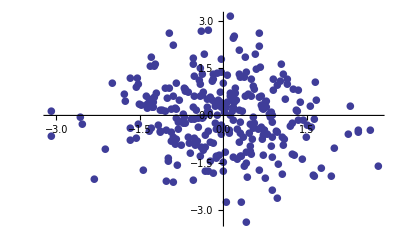

```mathematica
INcdf[x_]:=InverseCDF[NormalDistribution[],x];
X=INcdf[U]; Y=INcdf[V];
pl2=ListPlot[{X,Y}ᵀ,BaseStyle->{FontSize->14},PlotLabel->"Independent N(0,1)-random numbers",PlotRange->All,PlotMarkers->{Automatic,10}]
```

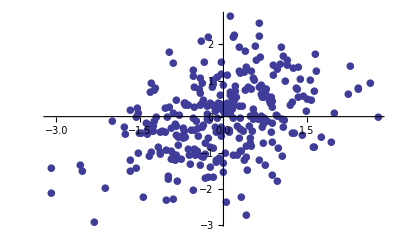

```mathematica
ρ=.5;
tX=X;
tY=ρ X+√(1-ρ^2) Y;
pl3=ListPlot[Transpose[{tX,tY}],BaseStyle->{FontSize->14},PlotLabel->"Correlated N(0,1)-random numbers (ρ=0.5)",PlotRange->All,PlotMarkers->{Automatic,10}]
```

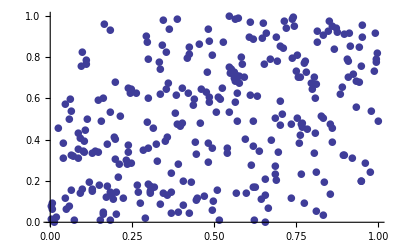

```mathematica
Ncdf[x_]:=CDF[NormalDistribution[],x];
tU=Ncdf[tX]; 
tV=Ncdf[tY];
pl4=ListPlot[{tU,tV}ᵀ,BaseStyle->{FontSize->14},PlotLabel->"U(0,1)-random numbers, Gaussian copula (ρ=0.5)",PlotRange->All,PlotMarkers->{Automatic,10},ImageSize->Scaled[1.0]]
```

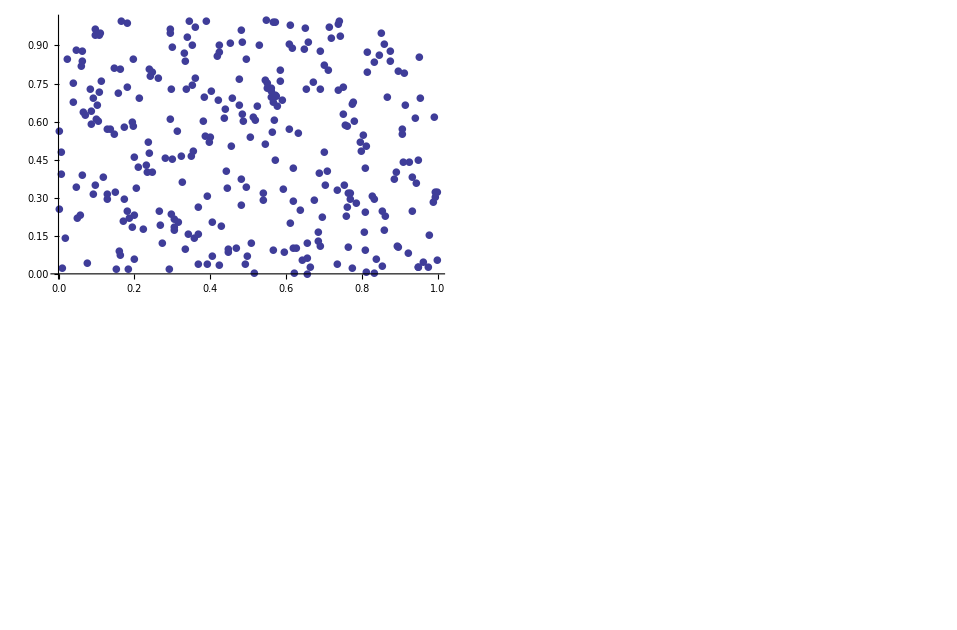

```mathematica
pl5=GraphicsGrid[{{pl1,pl2},{pl3,pl4}}]
```

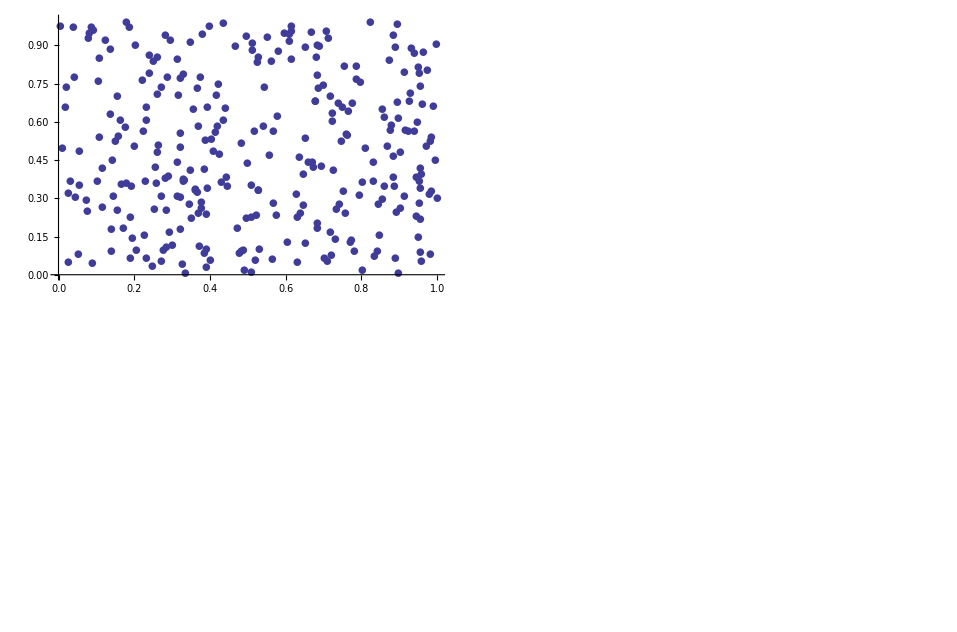

```mathematica
Export["~/Documents/tex/scripts/riskmodelling/pics/copulas/normal3.eps", pl5,ImageResolution->300]
```

~/Documents/tex/scripts/riskmodelling/pics/copulas/normal3.eps

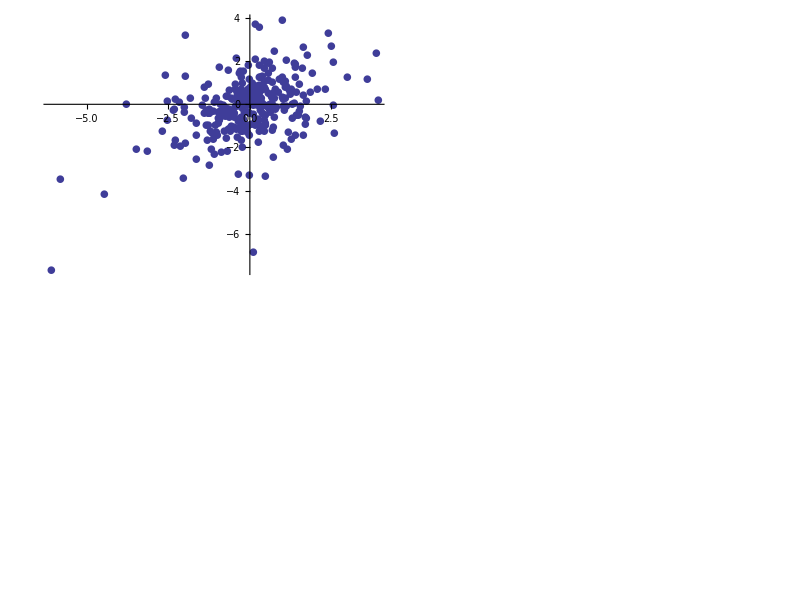
(-Graphics-)

```mathematica
Tcdf[x_,ν_]:=CDF[StudentTDistribution[ν],x];
pl4=Table[
W=RandomVariate[InverseGammaDistribution[ν/2,ν/2],500];
bX=Sqrt[W]tX;
bY=Sqrt[W] tY;
bU=Tcdf[bX,ν];
bV=Tcdf[bY,ν];
{ListPlot[{bX,bY}ᵀ,BaseStyle->{FontSize->14},PlotLabel->"t-distributed random numbers (ρ=0.5, ν=" <> ToString[ν] <>")",PlotRange->All,PlotMarkers->{Automatic,10},ImageSize->Scaled[1.0]],
ListPlot[{bU,bV}ᵀ,BaseStyle->{FontSize->14},PlotLabel->"U(0,1)-random numbers, t-copula (ρ=0.5, ν="<>ToString[ν]<>")",PlotRange->All,PlotMarkers->{Automatic,10},ImageSize->Scaled[1.0]]}
,{ν,{5,20}}]
```

```mathematica
Dimensions[pl4]
```

{2,2}

```mathematica
Export["~/Documents/tex/scripts/riskmodelling/pics/copulas/tcopula.eps",GraphicsGrid[pl4],ImageResolution->300];(*GraphicsGrid[{{pl4⟦1,All⟧},{pl4⟦2,All⟧}}]]*)
```

```mathematica
U=UniformDistribution[];(*G=RandomVariate[CopulaDistribution[{"GumbelHougaard", 2}, {U,U}],500];*)
```

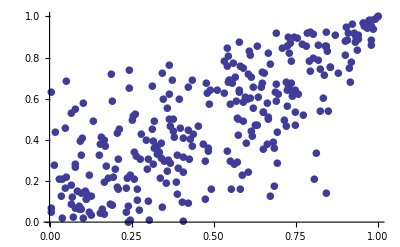
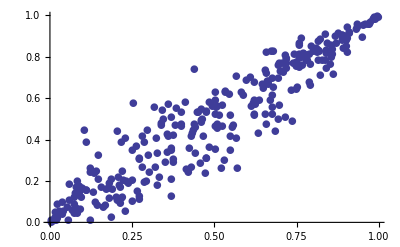

```mathematica
pl1=Table[ListPlot[RandomVariate[CopulaDistribution[{"GumbelHougaard", k}, {U,U}],500],BaseStyle->{FontSize->18},PlotLabel->StringJoin["U(0,1)-random numbers, Gumbel-copula (θ=", ToString[k], ")"],PlotRange->All,PlotMarkers->{Automatic,10},ImageSize->Scaled[1.0]],{k,{2,5}}]
```

```mathematica
(*Cl=RandomVariate[CopulaDistribution[{"Clayton", 1/3.2}, {U,U}],500];*)
```

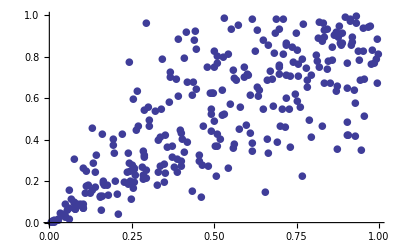
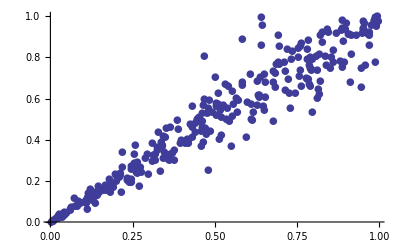

```mathematica
pl2=Table[ListPlot[RandomVariate[CopulaDistribution[{"Clayton", 1/k}, {U,U}],500],BaseStyle->{FontSize->18},PlotLabel->"U(0,1)-random numbers, Clayton-copula (θ=" <> ToString[k] <>")",PlotRange->All,PlotMarkers->{Automatic,10},ImageSize->Scaled[1.0]],{k,{3,10}}]
```

```mathematica
Export["~/Documents/tex/scripts/riskmodelling/pics/copulas/gumbel.eps",pl1,ImageResolution->300]
Export["~/Documents/tex/scripts/riskmodelling/pics/copulas/clayton.eps",pl2,ImageResolution->300]
```

~/Documents/tex/scripts/riskmodelling/pics/copulas/gumbel.eps

~/Documents/tex/scripts/riskmodelling/pics/copulas/clayton.eps

Clayton copula (see p. 224, McNeil):

```mathematica
U=RandomVariate[UniformDistribution[],500];
V=RandomVariate[UniformDistribution[],500];
```

```mathematica
θ=3;
V2=RandomVariate[GammaDistribution[1/θ,1],500];
```

```mathematica
Ghat[t_,θ_]:=(1+t)^(-1/θ);
UCl=Ghat[-Log[U]/V2,θ];
VCl=Ghat[-Log[V]/V2,θ];
```

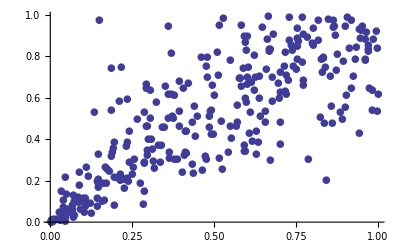

```mathematica
ListPlot[{UCl,VCl}ᵀ,BaseStyle->{FontSize->14},PlotLabel->"U(0,1)-random numbers, Clayton-copula (θ=3)",PlotRange->All,PlotMarkers->{Automatic,10},ImageSize->Scaled[1.0]]
```

Maximal correlation of two lognormally distributed random variables:

```mathematica
Exp[1]/((Exp[1]-1) Exp[1])
```

1/(ⅇ-1)

```mathematica
N[%]
```

0.581977

```mathematica
Mean[LogNormalDistribution[0,1]]^2/Variance[LogNormalDistribution[0,1]]
```

1/(ⅇ-1)

```mathematica
Exp[x] Exp[x]
```

ⅇ^(2 x)

```mathematica
Exp[1/2]^2
```

ⅇ

```mathematica
Mean[LogNormalDistribution[0,2σ]]
```

10.7258

```mathematica
Mean[LogNormalDistribution[0,1]] Mean[LogNormalDistribution[0,σ]]
```

2.9837

```mathematica
Simplify[Mean[LogNormalDistribution[0,2σ]]-Mean[LogNormalDistribution[0,1]] Mean[LogNormalDistribution[0,σ]]]
```

7.74211

```mathematica
Variance[LogNormalDistribution[0,1]]
```

(ⅇ-1) ⅇ

```mathematica
Variance[LogNormalDistribution[0,σ]]
```

7.45078

```mathematica
Simplify[Sqrt[Variance[LogNormalDistribution[0,1]] Variance[LogNormalDistribution[0,σ]]]]
```

5.89923

```mathematica
Simplify[(Mean[LogNormalDistribution[0, 1+σ]]-Mean[LogNormalDistribution[0,1]] Mean[LogNormalDistribution[0,σ]])/Sqrt[Variance[LogNormalDistribution[0,1]] Variance[LogNormalDistribution[0,σ]]]]
```

0.997319

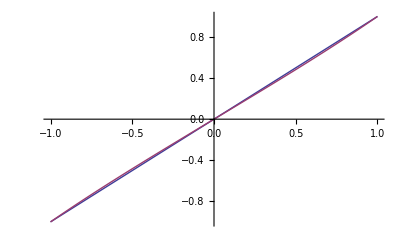

```mathematica
Plot[{ρ,(6 ArcSin[ρ/2])/π},{ρ,-1,1}]
```